```mathematica
polys=Subsets[Table[CompletePoly[k],{k,10}],{2}]
```

{{x,-x+x^2},{x,2 x-3 x^2+x^3},{x,-6 x+11 x^2-6 x^3+x^4},{x,24 x-50 x^2+35 x^3-10 x^4+x^5},{x,-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6},{x,720 x-1764 x^2+1624 x^3-735 x^4+175 x^5-21 x^6+x^7},{x,-5040 x+13068 x^2-13132 x^3+6769 x^4-1960 x^5+322 x^6-28 x^7+x^8},{x,40320 x-109584 x^2+118124 x^3-67284 x^4+22449 x^5-4536 x^6+546 x^7-36 x^8+x^9},{x,-362880 x+1026576 x^2-1172700 x^3+723680 x^4-269325 x^5+63273 x^6-9450 x^7+870 x^8-45 x^9+x^10},{-x+x^2,2 x-3 x^2+x^3},{-x+x^2,-6 x+11 x^2-6 x^3+x^4},{-x+x^2,24 x-50 x^2+35 x^3-10 x^4+x^5},{-x+x^2,-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6},{-x+x^2,720 x-1764 x^2+1624 x^3-735 x^4+175 x^5-21 x^6+x^7},{-x+x^2,-5040 x+13068 x^2-13132 x^3+6769 x^4-1960 x^5+322 x^6-28 x^7+x^8},{-x+x^2,40320 x-109584 x^2+118124 x^3-67284 x^4+22449 x^5-4536 x^6+546 x^7-36 x^8+x^9},{-x+x^2,-362880 x+1026576 x^2-1172700 x^3+723680 x^4-269325 x^5+63273 x^6-9450 x^7+870 x^8-45 x^9+x^10},{2 x-3 x^2+x^3,-6 x+11 x^2-6 x^3+x^4},{2 x-3 x^2+x^3,24 x-50 x^2+35 x^3-10 x^4+x^5},{2 x-3 x^2+x^3,-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6},{2 x-3 x^2+x^3,720 x-1764 x^2+1624 x^3-735 x^4+175 x^5-21 x^6+x^7},{2 x-3 x^2+x^3,-5040 x+13068 x^2-13132 x^3+6769 x^4-1960 x^5+322 x^6-28 x^7+x^8},{2 x-3 x^2+x^3,40320 x-109584 x^2+118124 x^3-67284 x^4+22449 x^5-4536 x^6+546 x^7-36 x^8+x^9},{2 x-3 x^2+x^3,-362880 x+1026576 x^2-1172700 x^3+723680 x^4-269325 x^5+63273 x^6-9450 x^7+870 x^8-45 x^9+x^10},{-6 x+11 x^2-6 x^3+x^4,24 x-50 x^2+35 x^3-10 x^4+x^5},{-6 x+11 x^2-6 x^3+x^4,-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6},{-6 x+11 x^2-6 x^3+x^4,720 x-1764 x^2+1624 x^3-735 x^4+175 x^5-21 x^6+x^7},{-6 x+11 x^2-6 x^3+x^4,-5040 x+13068 x^2-13132 x^3+6769 x^4-1960 x^5+322 x^6-28 x^7+x^8},{-6 x+11 x^2-6 x^3+x^4,40320 x-109584 x^2+118124 x^3-67284 x^4+22449 x^5-4536 x^6+546 x^7-36 x^8+x^9},{-6 x+11 x^2-6 x^3+x^4,-362880 x+1026576 x^2-1172700 x^3+723680 x^4-269325 x^5+63273 x^6-9450 x^7+870 x^8-45 x^9+x^10},{24 x-50 x^2+35 x^3-10 x^4+x^5,-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6},{24 x-50 x^2+35 x^3-10 x^4+x^5,720 x-1764 x^2+1624 x^3-735 x^4+175 x^5-21 x^6+x^7},{24 x-50 x^2+35 x^3-10 x^4+x^5,-5040 x+13068 x^2-13132 x^3+6769 x^4-1960 x^5+322 x^6-28 x^7+x^8},{24 x-50 x^2+35 x^3-10 x^4+x^5,40320 x-109584 x^2+118124 x^3-67284 x^4+22449 x^5-4536 x^6+546 x^7-36 x^8+x^9},{24 x-50 x^2+35 x^3-10 x^4+x^5,-362880 x+1026576 x^2-1172700 x^3+723680 x^4-269325 x^5+63273 x^6-9450 x^7+870 x^8-45 x^9+x^10},{-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6,720 x-1764 x^2+1624 x^3-735 x^4+175 x^5-21 x^6+x^7},{-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6,-5040 x+13068 x^2-13132 x^3+6769 x^4-1960 x^5+322 x^6-28 x^7+x^8},{-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6,40320 x-109584 x^2+118124 x^3-67284 x^4+22449 x^5-4536 x^6+546 x^7-36 x^8+x^9},{-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6,-362880 x+1026576 x^2-1172700 x^3+723680 x^4-269325 x^5+63273 x^6-9450 x^7+870 x^8-45 x^9+x^10},{720 x-1764 x^2+1624 x^3-735 x^4+175 x^5-21 x^6+x^7,-5040 x+13068 x^2-13132 x^3+6769 x^4-1960 x^5+322 x^6-28 x^7+x^8},{720 x-1764 x^2+1624 x^3-735 x^4+175 x^5-21 x^6+x^7,40320 x-109584 x^2+118124 x^3-67284 x^4+22449 x^5-4536 x^6+546 x^7-36 x^8+x^9},{720 x-1764 x^2+1624 x^3-735 x^4+175 x^5-21 x^6+x^7,-362880 x+1026576 x^2-1172700 x^3+723680 x^4-269325 x^5+63273 x^6-9450 x^7+870 x^8-45 x^9+x^10},{-5040 x+13068 x^2-13132 x^3+6769 x^4-1960 x^5+322 x^6-28 x^7+x^8,40320 x-109584 x^2+118124 x^3-67284 x^4+22449 x^5-4536 x^6+546 x^7-36 x^8+x^9},{-5040 x+13068 x^2-13132 x^3+6769 x^4-1960 x^5+322 x^6-28 x^7+x^8,-362880 x+1026576 x^2-1172700 x^3+723680 x^4-269325 x^5+63273 x^6-9450 x^7+870 x^8-45 x^9+x^10},{40320 x-109584 x^2+118124 x^3-67284 x^4+22449 x^5-4536 x^6+546 x^7-36 x^8+x^9,-362880 x+1026576 x^2-1172700 x^3+723680 x^4-269325 x^5+63273 x^6-9450 x^7+870 x^8-45 x^9+x^10}}

```mathematica
Clear[poplys]
```

```mathematica
CompletePoly[1]
```

x

```mathematica
poplys[max_]:=Flatten[Table[Map[Total,Subsets[Table[CompletePoly[k],{k,max}],l]],{l,max}]]
```

```mathematica
Map[Factor,poplys[4]]
```

{0,x,(-1+x) x,(-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,0,x,(-1+x) x,(-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,x^2,x (3-3 x+x^2),x (-5+11 x-6 x^2+x^3),(-1+x)^2 x,(-1+x) x (7-5 x+x^2),(-2+x)^2 (-1+x) x,0,x,(-1+x) x,(-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,x^2,x (3-3 x+x^2),x (-5+11 x-6 x^2+x^3),(-1+x)^2 x,(-1+x) x (7-5 x+x^2),(-2+x)^2 (-1+x) x,x (2-2 x+x^2),x (-6+12 x-6 x^2+x^3),x (-3+8 x-5 x^2+x^3),(-1+x) x (5-4 x+x^2),0,x,(-1+x) x,(-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,x^2,x (3-3 x+x^2),x (-5+11 x-6 x^2+x^3),(-1+x)^2 x,(-1+x) x (7-5 x+x^2),(-2+x)^2 (-1+x) x,x (2-2 x+x^2),x (-6+12 x-6 x^2+x^3),x (-3+8 x-5 x^2+x^3),(-1+x) x (5-4 x+x^2),x (-4+9 x-5 x^2+x^3)}

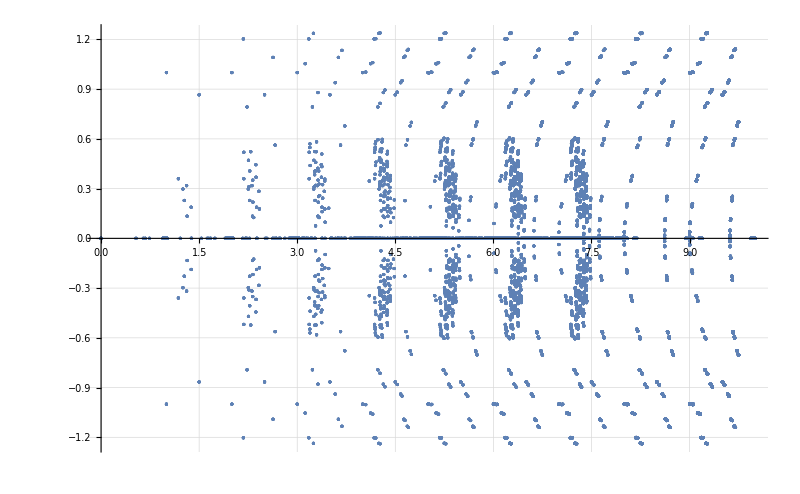

```mathematica
Monitor[ListPlot[Flatten[ParallelTable[Map[ReIm,ComplexExpand[x/.NSolve[pol==0,x]]],{pol,poplys[11]}],1],
GridLines->Automatic,  PlotRangeClipping->True, ImageSize->800],k]
```

```mathematica
ChromaticPolynomial[ReadGrof[20],x]//CompleteBaseCoeff//Reverse
```

{1,10,27,22,4,0,0,0,0}

```mathematica
DeleteDuplicates[Flatten[ParallelTable[Factor[ChromaticPolynomial[ReadGrof[k],x]],{k,Select[Range[10000],FileExistsQ[RootGrofsPath <> ToString[#] <> ".grof"]&]}],1]]
```

{(-3+x) (-2+x) (-1+x) x,(-3+x)^2 (-2+x) (-1+x) x,(-3+x)^3 (-2+x) (-1+x) x,(-3+x)^5 (-2+x) (-1+x) x,(-3+x)^2 (-2+x) (-1+x) x (-35+30 x-9 x^2+x^3),(-3+x)^2 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3),(-3+x) (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-2+x) (-1+x) x (-332+498 x-303 x^2+94 x^3-15 x^4+x^5),(-3+x)^6 (-2+x) (-1+x) x,(-3+x)^3 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3),(-3+x)^3 (-2+x) (-1+x) x (-35+30 x-9 x^2+x^3),(-3+x)^4 (-2+x) (-1+x) x (-35+30 x-9 x^2+x^3),(-3+x)^4 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3),(-3+x)^2 (-2+x) (-1+x) x (-398+553 x-317 x^2+95 x^3-15 x^4+x^5),(-3+x)^2 (-2+x) (-1+x) x (-422+570 x-320 x^2+95 x^3-15 x^4+x^5),(-3+x)^3 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-3+x) (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3) (-35+30 x-9 x^2+x^3),(-3+x)^2 (-2+x) (-1+x) x (-332+498 x-303 x^2+94 x^3-15 x^4+x^5),(-3+x)^2 (-2+x) (-1+x) x (-447+591 x-327 x^2+96 x^3-15 x^4+x^5),(-3+x)^2 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5),(-3+x)^7 (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3)^2,(-3+x)^2 (-2+x) (-1+x) x (-438+585 x-326 x^2+96 x^3-15 x^4+x^5),(-3+x) (-2+x) (-1+x) x (1496-2368 x+1619 x^2-620 x^3+141 x^4-18 x^5+x^6),(-3+x)^2 (-2+x) (-1+x) x (7-5 x+x^2) (-49+38 x-10 x^2+x^3),(-3+x) (-2+x) (-1+x) x (1199-2077 x+1525 x^2-610 x^3+141 x^4-18 x^5+x^6),(-3+x) (-2+x) (-1+x) x (1271-2152 x+1551 x^2-613 x^3+141 x^4-18 x^5+x^6),(-3+x) (-2+x) (-1+x) x (1385-2265 x+1588 x^2-617 x^3+141 x^4-18 x^5+x^6),(-3+x) (-2+x) (-1+x) x (1454-2330 x+1608 x^2-619 x^3+141 x^4-18 x^5+x^6),(-2+x) (-1+x) x (-3728+7603 x-6734 x^2+3371 x^3-1034 x^4+195 x^5-21 x^6+x^7),(-2+x) (-1+x) x (-3152+6787 x-6301 x^2+3269 x^3-1025 x^4+195 x^5-21 x^6+x^7),(-3+x)^8 (-2+x) (-1+x) x,(-3+x)^5 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3),(-3+x)^3 (-2+x) (-1+x) x (-332+498 x-303 x^2+94 x^3-15 x^4+x^5),(-3+x)^5 (-2+x) (-1+x) x (-35+30 x-9 x^2+x^3),(-3+x)^3 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5),(-3+x)^3 (-2+x) (-1+x) x (-398+553 x-317 x^2+95 x^3-15 x^4+x^5),(-3+x)^2 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3)^2,(-3+x)^4 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-3+x)^2 (-2+x) (-1+x) x (1271-2152 x+1551 x^2-613 x^3+141 x^4-18 x^5+x^6),(-3+x)^3 (-2+x) (-1+x) x (-438+585 x-326 x^2+96 x^3-15 x^4+x^5),(-3+x)^3 (-2+x) (-1+x) x (7-5 x+x^2) (-49+38 x-10 x^2+x^3),(-3+x) (-2+x) (-1+x) x (-3695+7610 x-6794 x^2+3413 x^3-1045 x^4+196 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (1199-2077 x+1525 x^2-610 x^3+141 x^4-18 x^5+x^6),(-3+x) (-2+x) (-1+x) x (-3962+7978 x-6986 x^2+3458 x^3-1049 x^4+196 x^5-21 x^6+x^7),(-3+x) (-2+x) (-1+x) x (-3152+6787 x-6301 x^2+3269 x^3-1025 x^4+195 x^5-21 x^6+x^7),(-3+x) (-2+x) (-1+x) x (-4382+8529 x-7258 x^2+3518 x^3-1054 x^4+196 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (1390-2285 x+1609 x^2-625 x^3+142 x^4-18 x^5+x^6),(-3+x) (-2+x) (-1+x) x (-3907+7891 x-6930 x^2+3441 x^3-1047 x^4+196 x^5-21 x^6+x^7),(-3+x) (-2+x) (-1+x) x (-4712+8939 x-7448 x^2+3557 x^3-1057 x^4+196 x^5-21 x^6+x^7),(-3+x) (-2+x) (-1+x) x (-4508+8685 x-7329 x^2+3532 x^3-1055 x^4+196 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (1385-2265 x+1588 x^2-617 x^3+141 x^4-18 x^5+x^6),(-3+x) (-2+x) (-1+x) x (-3728+7603 x-6734 x^2+3371 x^3-1034 x^4+195 x^5-21 x^6+x^7),(-3+x) (-2+x) (-1+x) x (-4247+8337 x-7149 x^2+3489 x^3-1051 x^4+196 x^5-21 x^6+x^7),(-3+x) (-2+x) (-1+x) x (-4910+9170 x-7545 x^2+3574 x^3-1058 x^4+196 x^5-21 x^6+x^7),(-3+x) (-2+x) (-1+x) x (-4043+8086 x-7040 x^2+3470 x^3-1050 x^4+196 x^5-21 x^6+x^7),(-2+x) (-1+x) x (13360-30250 x+30418 x^2-17818 x^3+6674 x^4-1641 x^5+259 x^6-24 x^7+x^8),(-3+x) (-2+x) (-1+x) x (-3195+6880 x-6387 x^2+3310 x^3-1035 x^4+196 x^5-21 x^6+x^7),(-3+x)^6 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3),(-3+x)^9 (-2+x) (-1+x) x,(-3+x)^4 (-2+x) (-1+x) x (-332+498 x-303 x^2+94 x^3-15 x^4+x^5),(-3+x)^6 (-2+x) (-1+x) x (-35+30 x-9 x^2+x^3),(-3+x)^4 (-2+x) (-1+x) x (-383+542 x-315 x^2+95 x^3-15 x^4+x^5),(-3+x)^5 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),(-3+x)^3 (-2+x) (-1+x) x (1199-2077 x+1525 x^2-610 x^3+141 x^4-18 x^5+x^6),(-3+x)^3 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3)^2,(-3+x)^3 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3) (-35+30 x-9 x^2+x^3),(-3+x)^3 (-2+x) (-1+x) x (1271-2152 x+1551 x^2-613 x^3+141 x^4-18 x^5+x^6),(-3+x)^3 (-2+x) (-1+x) x (1390-2285 x+1609 x^2-625 x^3+142 x^4-18 x^5+x^6),(-3+x)^2 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3) (119-133 x+58 x^2-12 x^3+x^4),(-3+x)^4 (-2+x) (-1+x) x (-398+553 x-317 x^2+95 x^3-15 x^4+x^5),(-3+x)^3 (-2+x) (-1+x) x (1385-2265 x+1588 x^2-617 x^3+141 x^4-18 x^5+x^6),(-3+x)^4 (-2+x) (-1+x) x (-438+585 x-326 x^2+96 x^3-15 x^4+x^5),(-3+x)^4 (-2+x) (-1+x) x (-447+591 x-327 x^2+96 x^3-15 x^4+x^5),(-3+x)^2 (-2+x) (-1+x) x (-3907+7891 x-6930 x^2+3441 x^3-1047 x^4+196 x^5-21 x^6+x^7),(-3+x)^4 (-2+x) (-1+x) x (7-5 x+x^2) (-49+38 x-10 x^2+x^3),(-3+x) (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3) (-332+498 x-303 x^2+94 x^3-15 x^4+x^5),(-3+x)^2 (-2+x) (-1+x) x (-4298+8408 x-7188 x^2+3499 x^3-1052 x^4+196 x^5-21 x^6+x^7),(-3+x)^4 (-2+x) (-1+x) x (-422+570 x-320 x^2+95 x^3-15 x^4+x^5),(-3+x)^3 (-2+x) (-1+x) x (-35+30 x-9 x^2+x^3)^2,(-3+x)^2 (-2+x) (-1+x) x (-3728+7603 x-6734 x^2+3371 x^3-1034 x^4+195 x^5-21 x^6+x^7),(-3+x) (-2+x) (-1+x) x (13559-30728 x+30924 x^2-18106 x^3+6765 x^4-1656 x^5+260 x^6-24 x^7+x^8),(-3+x)^3 (-2+x) (-1+x) x (1459-2350 x+1629 x^2-627 x^3+142 x^4-18 x^5+x^6),(-3+x) (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3) (-383+542 x-315 x^2+95 x^3-15 x^4+x^5),(-3+x)^2 (-2+x) (-1+x) x (-35+30 x-9 x^2+x^3) (119-133 x+58 x^2-12 x^3+x^4),(-3+x)^3 (-2+x) (-1+x) x (1454-2330 x+1608 x^2-619 x^3+141 x^4-18 x^5+x^6),(-3+x)^3 (-2+x) (-1+x) x (1501-2388 x+1640 x^2-628 x^3+142 x^4-18 x^5+x^6),(-3+x)^2 (-2+x) (-1+x) x (-4247+8337 x-7149 x^2+3489 x^3-1051 x^4+196 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (-4925+9235 x-7628 x^2+3619 x^3-1069 x^4+197 x^5-21 x^6+x^7),(-3+x)^3 (-2+x) (-1+x) x (1569-2450 x+1659 x^2-630 x^3+142 x^4-18 x^5+x^6),(-3+x)^2 (-2+x) (-1+x) x (-5033+9316 x-7610 x^2+3587 x^3-1059 x^4+196 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (-4910+9170 x-7545 x^2+3574 x^3-1058 x^4+196 x^5-21 x^6+x^7),(-3+x)^3 (-2+x) (-1+x) x (1496-2368 x+1619 x^2-620 x^3+141 x^4-18 x^5+x^6),(-3+x)^2 (-2+x) (-1+x) x (-4603+8855 x-7465 x^2+3589 x^3-1067 x^4+197 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (-4043+8086 x-7040 x^2+3470 x^3-1050 x^4+196 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (-3962+7978 x-6986 x^2+3458 x^3-1049 x^4+196 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (-4508+8685 x-7329 x^2+3532 x^3-1055 x^4+196 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (-4382+8529 x-7258 x^2+3518 x^3-1054 x^4+196 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (-4712+8939 x-7448 x^2+3557 x^3-1057 x^4+196 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (-4852+9157 x-7601 x^2+3616 x^3-1069 x^4+197 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (10-6 x+x^2) (-465+612 x-335 x^2+97 x^3-15 x^4+x^5),(-3+x) (-2+x) (-1+x) x (16346-35047 x+33629 x^2-18964 x^3+6903 x^4-1665 x^5+260 x^6-24 x^7+x^8),(-3+x) (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3) (-398+553 x-317 x^2+95 x^3-15 x^4+x^5),(-3+x)^2 (-2+x) (-1+x) x (-5053+9401 x-7714 x^2+3640 x^3-1071 x^4+197 x^5-21 x^6+x^7),(-3+x) (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3) (-422+570 x-320 x^2+95 x^3-15 x^4+x^5),(-3+x)^2 (-2+x) (-1+x) x (-5048+9381 x-7693 x^2+3632 x^3-1070 x^4+197 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (-5248+9622 x-7805 x^2+3656 x^3-1072 x^4+197 x^5-21 x^6+x^7),(-3+x) (-2+x) (-1+x) x (-35+30 x-9 x^2+x^3) (-332+498 x-303 x^2+94 x^3-15 x^4+x^5),(-3+x)^2 (-2+x) (-1+x) x (-4847+9137 x-7580 x^2+3608 x^3-1068 x^4+197 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (-4832+9072 x-7497 x^2+3563 x^3-1057 x^4+196 x^5-21 x^6+x^7),(-3+x) (-2+x) (-1+x) x (14171-31694 x+31535 x^2-18300 x^3+6796 x^4-1658 x^5+260 x^6-24 x^7+x^8),(-3+x)^2 (-2+x) (-1+x) x (-5127+9483 x-7745 x^2+3644 x^3-1071 x^4+197 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (-5370+9765 x-7869 x^2+3669 x^3-1073 x^4+197 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (-4583+8770 x-7361 x^2+3536 x^3-1055 x^4+196 x^5-21 x^6+x^7),(-3+x)^2 (-2+x) (-1+x) x (-4803+9093 x-7567 x^2+3607 x^3-1068 x^4+197 x^5-21 x^6+x^7),(-3+x) (-2+x) (-1+x) x (13799-31123 x+31188 x^2-18195 x^3+6780 x^4-1657 x^5+260 x^6-24 x^7+x^8),(-3+x) (-2+x) (-1+x) x (15149-33211 x+32481 x^2-18597 x^3+6843 x^4-1661 x^5+260 x^6-24 x^7+x^8),(-3+x) (-2+x) (-1+x) x (18185-37625 x+35058 x^2-19357 x^3+6957 x^4-1668 x^5+260 x^6-24 x^7+x^8),(-3+x)^2 (-2+x) (-1+x) x (-5228+9537 x-7701 x^2+3603 x^3-1060 x^4+196 x^5-21 x^6+x^7),(-3+x) (-2+x) (-1+x) x (17054-36051 x+34188 x^2-19116 x^3+6923 x^4-1666 x^5+260 x^6-24 x^7+x^8),(-3+x)^2 (-2+x) (-1+x) x (-5562+9976 x-7954 x^2+3684 x^3-1074 x^4+197 x^5-21 x^6+x^7),(-3+x) (-2+x) (-1+x) x (15536-33850 x+32921 x^2-18753 x^3+6871 x^4-1663 x^5+260 x^6-24 x^7+x^8),(-3+x)^7 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3)}